## 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{x,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"k","y"},BaseStyle->{FontSize->20}]
```

## 1) Infimum and supremum

```mathematica
Subscript[M, 1]=(-4,-3]
```

```mathematica
Subscript[M, 2]={x∈ℚ|x^2<2}
```

```mathematica
Subscript[M, 3]={1,1/2,1/3,1/4,...}
```

Solution

## M_1

```mathematica
inf Subscript[M, 1]=-4, sup Subscript[M, 1]=-3, no min, max Subscript[M, 1]=-3
```

## M_2

```mathematica
inf Subscript[M, 2]=-√2, sup Subscript[M, 2]=√2, no min, no max
```

```mathematica
x^2<2⇒Abs[x]<√2
```

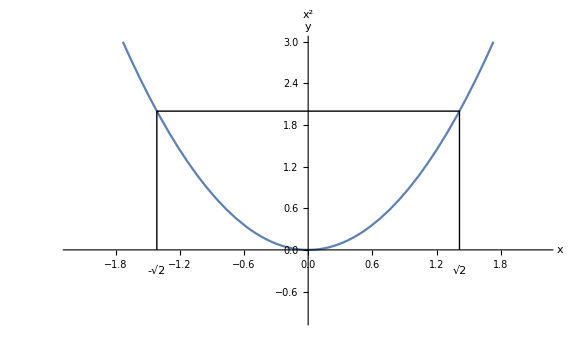

```mathematica
plotFun[x^2,{{-2.2,2.2},{-1,3}},{Line[{{√2,0},{√2,2},{-√2,2},{-√2,0}}],Text[√2,{√2,-.3}],Text[-√2,{-√2,-.3}]},"x^2"]
```

## M_3

```mathematica
inf Subscript[M, 3]=0, sup Subscript[M, 3]=1, no min, max Subscript[M, 3]=1
```

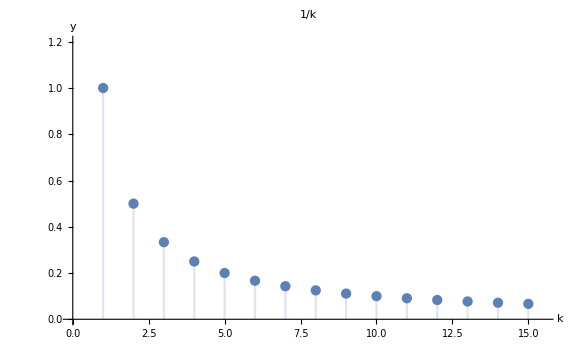

```mathematica
discPlotFun[1/x,{1,15},{{0,15.5},{0,1.2}},{},"1/k"]
```

## 2) Complex numbers

```mathematica
z=1/(1+2ⅈ)
```

Useful formulas:

Simplification formula

```mathematica
(a+b)(a-b)=a^2-b^2
```

Real and imaginary parts

```mathematica
z=Re(z)+ⅈ Im(z)
```

Polar form of a complex number

```mathematica
z=Abs[z] ⅇ^(ⅈ φ)
```

```mathematica
tan(φ)=(Im(φ))/(Re(φ))
```

```mathematica
Abs[z]^2=(Re(φ))^2+(Im(φ))^2
```

```mathematica
Abs[z]^2=z*z
```

Re and Im parts

```mathematica
1/(1+2ⅈ)==1/(1+2ⅈ)(1-2ⅈ)/(1-2ⅈ)==(1-2ⅈ)/(1^2-(2ⅈ)^2)==(1-2ⅈ)/5==1/5+(-2/5)ⅈ
```

Polar form

```mathematica
Abs[z]^2==(1/5)^2+(-2/5)^2==5/25==1/5  ⇒  Abs[z]==1/(√5)
```

```mathematica
tan(φ)==(-2/5)/(1/5)==-2  ⇒  φ==-tan^-1(2)
```

Graphically

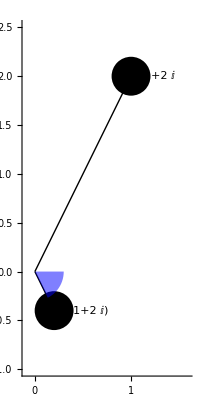

```mathematica
Framed@Graphics[{{PointSize[.07],Point[{ReIm[1+2I],ReIm[1/(1+2I)]}],Line[{{{0,0},ReIm[1+2I]},{{0,0},ReIm[1/(1+2I)]}}]},{Blue,Opacity[.5],Disk[{0,0},.3,{0,-ArcTan[2]}]},{Black,Style[Text[HoldForm@(1/(1+2I))//TraditionalForm,{.5,-.4}],20],Style[Text[HoldForm@(1+2I)//TraditionalForm,{1.3,2}],20]}},Axes->True,PlotRange->{{-.1,1.6},{-1,2.5}}]
```

## 3) Mathematical induction

```mathematica
∑_(k=0)^n (2 k+1)^2==((1+n)(1+2n)(3+2n))/3
```

Solution

Initial step

```mathematica
n==0:
```

```mathematica
LHS=∑_(k=0)^0 (2 k+1)^2=1
```

```mathematica
RHS=((1+0)(1+2 0)(3+2 0))/3=1
```

Induction step

```mathematica
n->n+1:
```

```mathematica
LHS==∑_(k=0)^(n+1) (2 k+1)^2==∑_(k=0)^n (2 k+1)^2+(2 (n+1)+1)^2==((1+n)(1+2n)(3+2n))/3+(2 n+3)^2==(2n+3)/3((1+n)(1+2n)+3(2 n+3))==(2n+3)/3(2 n^2+9n+10)
```

```mathematica
RHS==((1+(n+1))(1+2(n+1))(3+2(n+1)))/3==((n+2)(2n+3)(2n+5))/3==((2n+3)(2 n^2+9n+10))/3
```

## 4) Subtraction of sums

```mathematica
∑_(k=0)^n (2 k+1)^3-∑_(k=0)^(n+1) (2 k-1)^3
```

Useful formulas:

Shift summation index

```mathematica
∑_(k=0)^(n+1) Subscript[a, k]==∑_(k=-1)^n Subscript[a, k+1]
```

Subtraction of sums

```mathematica
∑_(k=0)^n Subscript[b, k]-∑_(k=-1)^n Subscript[b, k]==∑_(k=0)^n Subscript[b, k]-(Subscript[b, -1]+∑_(k=0)^n Subscript[b, k])==-Subscript[b, -1]
```

Solution

```mathematica
∑_(k=0)^n (2 k+1)^3-∑_(k=0)^(n+1) (2 k-1)^3==∑_(k=0)^n (2 k+1)^3-∑_(k=-1)^n (2 k+1)^3==-(2 (-1)+1)^3==1
```

## 5) Complex roots

z ∈ ℂ

```mathematica
z^6=2
```

Useful formulas:

Polar form of a complex number

```mathematica
z=Abs[z] ⅇ^(ⅈ φ)
```

Equality of complex exponentials

```mathematica
ⅇ^(ⅈ α)==ⅇ^(ⅈ β)⇔α≡β mod 2π
```

Solution

```mathematica
z^6==ⅇ^(ⅈ 6 φ) Abs[z]^6==2 ⅇ^(ⅈ 2 π k)
```

```mathematica
Abs[z]^6==2∧ⅇ^(ⅈ 6 φ)==ⅇ^(ⅈ 2 π k)
```

```mathematica
Abs[z]==2^(1/6)∧6 φ==2 π k
```

```mathematica
φ==π/3 k       k=0,1,2,3,4,5
```

Two real solutions:

```mathematica
z=±2^(1/6)=±1.122462048309373
```

Graphically

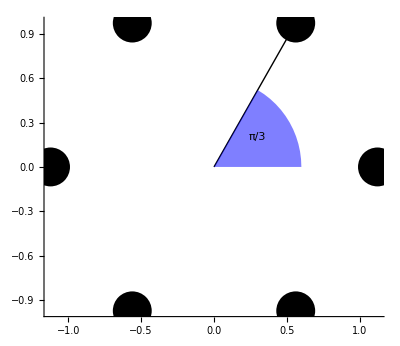

```mathematica
Framed@Graphics[{{PointSize[.07],Point[CirclePoints[2^(1/6),6]],Line[{{0,0},CirclePoints[2^(1/6),6][[3]]}]},{Blue,Opacity[.5],Disk[{0,0},.6,{0,π/3}]},{Black,Style[Text[π/3//TraditionalForm,{.3,.2}],20]}},Axes->True,PlotRange->1.2]
```

## 6) Triangle inequality

```mathematica
z,w∈ℂ
```

```mathematica
|z+w|≤|z|+|w|
```

Useful formulas:

```mathematica
Re z≤Abs[z]
```

Solution

```mathematica
Abs[w+z]^2==(w+z) Conjugate[(w+z)]==Abs[w]^2+Abs[z]^2+2 Re (w Conjugate[z])≤2 Abs[w Conjugate[z]]+Abs[w]^2+Abs[z]^2==2 Abs[w] Abs[z]+Abs[w]^2+Abs[z]^2==(Abs[w]+Abs[z])^2
```